```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/limit_cycles/systems/2";
SetDirectory[workingdirectory];
matrixfilenamesA="MATOUTB"
matrixfilenamesB="MATOUTV"
strA=OpenRead[matrixfilenamesA,BinaryFormat->True];
strB=OpenRead[matrixfilenamesB,BinaryFormat->True];
headmarker=BinaryRead[strA,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[strA,"Real64",ByteOrdering->$ByteOrdering];

headmarker=BinaryRead[strB,"Integer32",ByteOrdering->$ByteOrdering];
EvecMat=BinaryReadList[strB,"Real64",ByteOrdering->$ByteOrdering];

JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];
Close[str];

normRGM=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];hamRGM=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];eveRGM=ArrayReshape[EvecMat,{JbasisDim,JbasisDim}];

{evalMM,eveMM}=Eigensystem[{hamRGM,normRGM}];

Print["NORM = ",normRGM//MatrixForm];
Print["H    = ",hamRGM//MatrixForm];

Print["E_n   = ",evalMM//MatrixForm];
```

MATOUTB

MATOUTV

NORM = (0.00852342 | 0.0153984 | 0.0166212 | 0.0217184 | 0.0237003
0.0153984 | 0.041464 | 0.048252 | 0.0884522 | 0.111733
0.0166212 | 0.048252 | 0.0571177 | 0.11475 | 0.152185
0.0217184 | 0.0884522 | 0.11475 | 0.440585 | 0.999225
0.0237003 | 0.111733 | 0.152185 | 0.999225 | 6.97419)

H    = (1.51287 | 0.360102 | -0.0529148 | -2.41508 | -3.60399
0.360102 | 1.39828 | 1.37115 | -1.62028 | -5.50242
-0.0529148 | 1.37115 | 1.52184 | -0.911462 | -5.58887
-2.41508 | -1.62028 | -0.911462 | 5.47012 | -0.362443
-3.60399 | -5.50242 | -5.58887 | -0.362443 | 24.9333)

E_n   = (882.978
320.032
87.796
12.5844
-2.14186)

MATHEMATICA returns the solution to A·Z^T=B·Z^Tλ
with the Eigenvalue matrix (Z) not normalized!

```mathematica
Print["Z·N·Z^T=",Chop[eveMM.normRGM.Transpose[eveMM]]//MatrixForm]
Print["Z·H·Z^T=",Chop[eveMM.hamRGM.Transpose[eveMM]]//MatrixForm]
Print["(Z·N·Z^T)^-1(Z·H·Z^T)=",Chop[eveMM.hamRGM.Transpose[eveMM].Inverse[eveMM.normRGM.Transpose[eveMM]]]//MatrixForm]
```

Z·N·Z^T=(0.0000884597 | 0 | 0 | 0 | 0
0 | 0.000140126 | 0 | 0 | 0
0 | 0 | 0.00102528 | 0 | 0
0 | 0 | 0 | 0.0552314 | 0
0 | 0 | 0 | 0 | 0.409796)

Z·H·Z^T=(0.078108 | 0 | 0 | 0 | 0
0 | 0.0448447 | 0 | 0 | 0
0 | 0 | 0.0900156 | 0 | 0
0 | 0 | 0 | 0.695057 | 0
0 | 0 | 0 | 0 | -0.877728)

(Z·N·Z^T)^-1(Z·H·Z^T)=(882.978 | 0 | 0 | 0 | 0
0 | 320.032 | 0 | 0 | 0
0 | 0 | 87.796 | 0 | 0
0 | 0 | 0 | 12.5844 | 0
0 | 0 | 0 | 0 | -2.14186)

DSYGVX return the solution to A·Z=λ·B·Z
with the Eigenvalue matrix (Z) normalized as Z·N·Z^T=1

```mathematica
Print["Z·N·Z^T=",Chop[eveRGM.normRGM.Transpose[eveRGM]]//MatrixForm]
Print["Z·H·Z^T=",Chop[eveRGM.hamRGM.Transpose[eveRGM]]//MatrixForm]
```

Z·N·Z^T=(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

Z·H·Z^T=(-2.14186 | 0 | 0 | 0 | 0
0 | 12.5844 | 0 | 0 | 0
0 | 0 | 87.796 | 0 | 0
0 | 0 | 0 | 320.032 | 0
0 | 0 | 0 | 0 | 882.978)

```mathematica
α=0.102951;
rgmNormElement=1/8 √(π/(2 α^3))
```

4.74268

```mathematica
Integrate[r^2 Exp[-β r^2],{r,0,Infinity}]
```

ConditionalExpression[(√π)/(4 β^(3/2)),Re[β]>0]

```mathematica
eveRGM//MatrixForm
```

(-1.26453 | -0.348608 | -0.610422 | -0.548559 | -0.214825
0.800295 | 3.1274 | -2.33625 | 1.43472 | -0.409952
4.13057 | -20.249 | 23.2219 | -2.99461 | 0.187807
3.6888 | -62.8361 | 56.2977 | -2.23919 | 0.0959108
34.2664 | -80.5377 | 60.3498 | -1.40226 | 0.0552867)

```mathematica
coff={-0.43083,-0.87613,-2.4863, 1.9687,-1.0413, 1.7227,-1.7232,-0.073333};
width={9.8547, 5.9201, 1.7275, 1.431, 0.67123, 0.30377, 0.26105, 0.032217};
coffs={-3.1158,4.6411,-3.1364,-0.51875,-0.75687,0.64943,-0.62474,-0.092049};
widths={7.8993,6.61,5.2779,1.7705,0.63777,0.40185,0.26105,0.039175};
wfkt[rr_]:=Total[Table[coffs[[n]] Exp[-widths[[n]] rr^2],{n,Length[coffs]}]];
wfkt2[rr_]:=Total[Table[coff[[n]] Exp[-width[[n]] rr^2],{n,Length[coff]}]];
```

```mathematica
wfkt[1]
wfkt2[1]
```

-0.634402

-0.632676

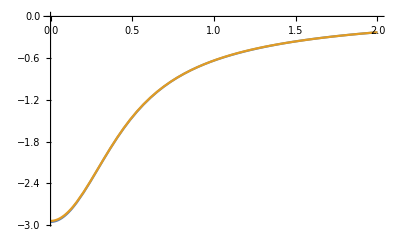

```mathematica
Plot[{wfkt[x],wfkt2[x]},{x,0,2}]
```